# Lesson 6: Continuity

#### Overview

The limit of a polynomial is just the value of the polynomial.

```mathematica
f[x_]:= 2 x^4-3x-9
```

```mathematica
Limit[f[x],x->a]
```

-9-3 a+2 a^4

A function whose limit at any point is just the value of the function at that point is called continuous.

## Continuous Functions

```mathematica
f[x_]:= x^2-x+1
```

```mathematica
f[1] == Limit[f[x],x->1]
```

True

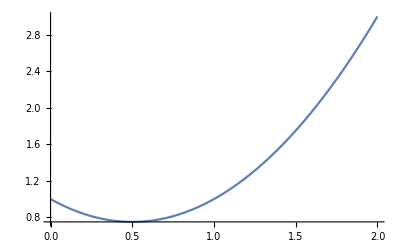

```mathematica
Plot[f[x],{x,0,2}]
```

## Polynomials and Rationals

```mathematica
f[x_]:= 5 x^3
g[x_]:=x/(x+1)
```

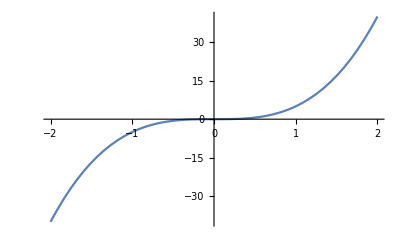

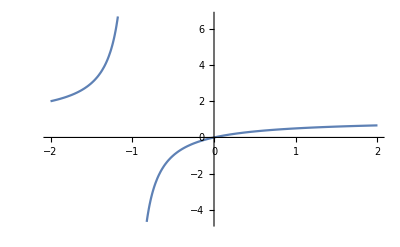

```mathematica
Plot[f[x],{x,-2,2}]
Plot[g[x],{x,-2,2}]
```

## Discontinuous Functions 1

```mathematica
f[x_]:= (x^2-5x+4)/(x-1)
g[x_]:= Piecewise[{{-2, x==1}}, (x^2-5x+4)/(x-1)]
```

```mathematica
f[1] // Quiet
```

Indeterminate

```mathematica
{g[1], Limit[g[x], x->1]}
```

{-2,-3}

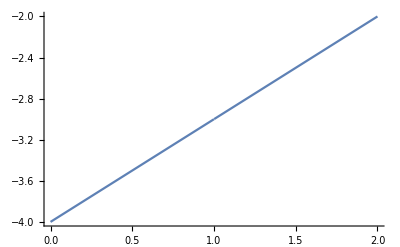
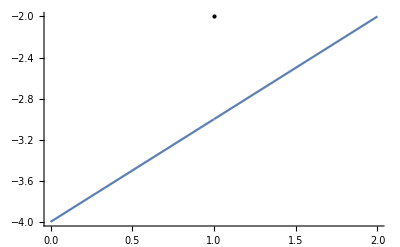

```mathematica
{Plot[f[x],{x,0,2}], Plot[g[x], {x,0,2}, Epilog->{Black, PointSize[Large], Point[{1,g[1]}]}]}
```

## Discontinuous Functions 2

```mathematica
f[x_]:= Piecewise[{{0,x==0}},1/x^4]
g[x_]:=Floor[x]
```

```mathematica
{Limit[f[x],x->0],f[0]}
```

```mathematica
{∞,0}
```

```mathematica
g[0]
```

0

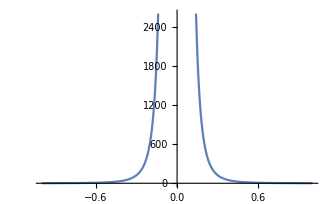
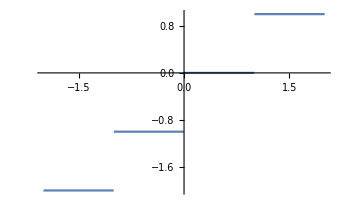

```mathematica
{Plot[f[x],{x,-1,1}], Plot[g[x],{x,-2,2},Axes->{False,True}]}
```

## Continuity from different directions

```mathematica
Limit[Floor[x],x->0, Direction->"FromAbove"]==Floor[0]
```

True

```mathematica
Limit[Floor[x],x->0,Direction->"FromBelow"]==Floor[0]
```

False

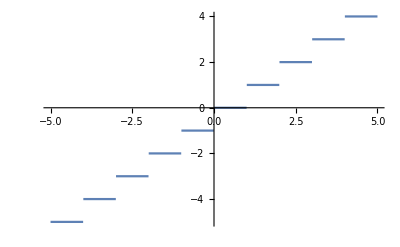

```mathematica
Plot[Floor[x],{x,-5,5}]
```

## Root Functions

```mathematica
f[x_]:=Sqrt[x]
```

```mathematica
{Limit[f[x],x->9], Sqrt[9]}
```

{3,3}

```mathematica
Sqrt[-1]
```

ⅈ

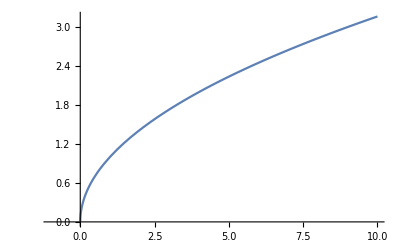

```mathematica
Plot[f[x],{x,-1,10}]
```

## Trigonometric Functions

```mathematica
Limit[Sin[x],x->0]==Sin[0]
```

True

```mathematica
Limit[Cos[x],x->0]==Cos[0]
```

True

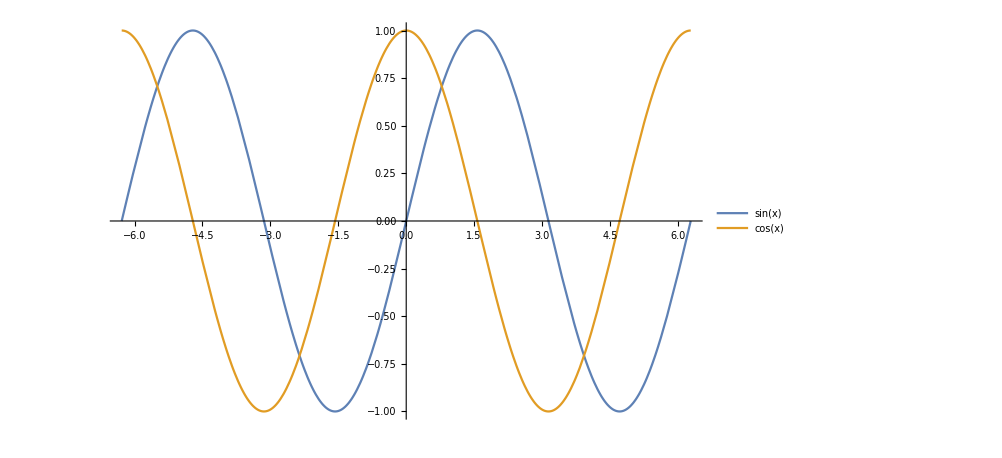

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2π,2π},PlotLegends->"Expressions"]
```

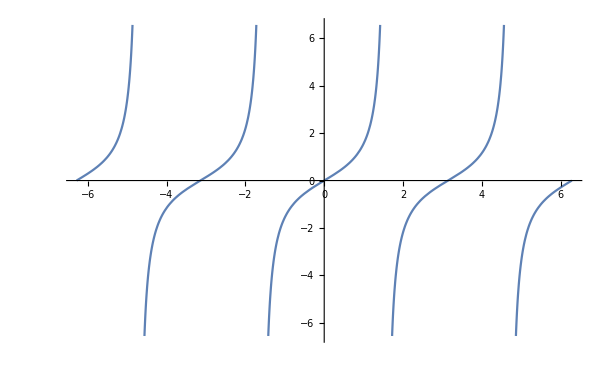

```mathematica
Plot[Tan[x],{x,-2π,2π}]
```

## Continuity Laws

```mathematica
f[x_]:=Cos[x]/(2+Sin[x])
```

```mathematica
f[π]
```

-1/2

```mathematica
Limit[f[x],x->π]==-1/2
```

True

## Compositions

```mathematica
HoldForm[Limit[f[g[x]],x->a] == f[Limit[g[x],x->a]]]//TraditionalForm
```

f(g(x))xa==f(g(x)xa)

```mathematica
f[x_]:=Cos[x^2-7x+10]
```

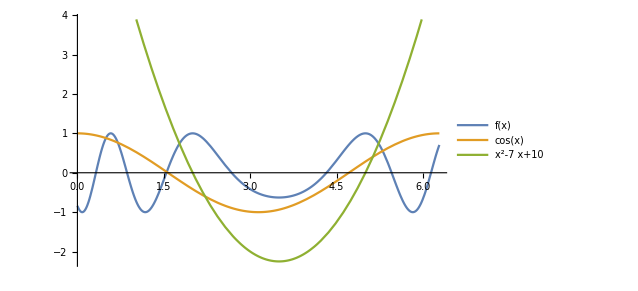

```mathematica
Plot[{f[x],Cos[x],x^2-7x+10},{x,0,2π},PlotLegends->"Expressions"]
```

```mathematica
{f[π],Limit[f[x],x-> π]==f[π]}
```

{-Cos[10+π^2],True}

## Intermediate Value Theorem

```mathematica
f[x_]:=3 x^3-5 x^2+2x-3
```

```mathematica
f[{1,2}]
```

{-3,5}

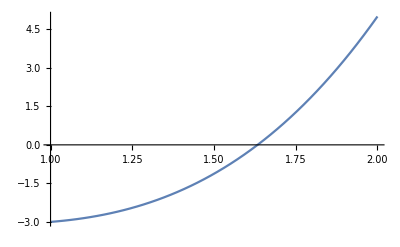

```mathematica
Plot[f[x],{x,1,2}]
```

```mathematica
Solve[f[x]==0,x,Reals]//N
```

{{x→1.63334}}